```mathematica
Quit[];
```

## Definitions

```mathematica
mypath=NotebookDirectory[];
Get[mypath<>"/setting_sigma.m"]
(*?Sigmaqqbar
?Sigmagg*)
```

```mathematica
ResetCuba[] := Module[{pwd = Directory[]},
  SetDirectory["/home/sapeta/heptools/Cuba-4.2/bin"];
  Install["Vegas"];
  Install["Cuhre"];
  Install["Suave"];
  SetDirectory[pwd];
  ]
```

```mathematica
Theta[x_]:=Module[{},If[x>0,1,0]]
```

Replacements:

```mathematica
ReplBetaXs={xs->(1-beta)/(1+beta),beta-> Sqrt[1-(4 mt^2)/M^2] };
ReplXs = {xs-> (1-βt)/(1+βt)};
ReplHShs={HSqq00-> hsqq00,HSqq11-> hsqq11,HSqq10-> hsqq10,HSqq21-> hsqq21,HSqq22-> hsqq22};
(*ReplPqq2={Pqq2[z]:>   (pqqV[z]+pqqbV[z]+2 nf pqqS[z])//Simplify};*)
(*ReplPqq2={Pqq2[z]:>   (pqqV[z])//Simplify};*)
(*ReplPqq2={Pqq2[z]:>  (pqqV[z]+ pqqS[z])//Simplify};*)
(*ReplPqq2={Pqq2[z]:>  (pqqV[z]+pqqbV[z]+ pqqS[z])//Simplify};*)
(*ReplPqq2={Pqq2[z]:>  8(PqqVreg[z])//Simplify};*)
(*ReplPqq2={Pqq2[z]:> 8(PqqVreg[z]+PqqSreg[z])//Simplify};*)
ReplPqq2={Pqq2[z]:> 0};

ReplForC={μ-> mu,βt-> beta};
ReplNumbers={β0-> 11/3 CA-4/3 TF nf,CA-> 3, Nc-> 3, CF-> 4/3, nf-> 5, TF-> 1/2};
```

```mathematica
ReplNotationIinitial={Log[t1^2/(M^2 mt^2)]->2Log[-t1/(M mt)],Li2[a_]-> PolyLog[2,a]};
ReplLogs={Log[-t1/mt^2]-> Lt1,Log[(t1 u1)/(M^2 mt^2)]-> Lt1u1,Log[Cos[θ/2]]-> LC,Log[μ^2/mt^2]-> Lmu,Log[(M^2+t1)/mt^2]-> Lt1M,Log[xs]-> LXS,Log[1+xs]-> LXSp1,Log[1-xs]-> LXSm1,Log[-t1/(M mt)]-> L13,Log[-u1/(M mt)]-> L23,Log[1-1/xs^2]-> LdXS};
ReplPolyLogs={PolyLog[2,1+t1/mt^2]-> L2t1,PolyLog[2,1-(t1 u1)/(M^2 mt^2)]-> Li2t1u1,PolyLog[2,-xs Tan[θ/2]^2] -> Li2Tn,PolyLog[2,-Tan[θ/2]^2/xs] -> Li2Td,PolyLog[2,-(M^2-mt^2+t1)/mt^2]-> Li21M,PolyLog[2,xs]-> Li2pXS,PolyLog[2,-xs]-> Li2mXS,PolyLog[3,1/xs^2]-> Li3dXS,PolyLog[2,1/xs^2]-> Li2dXS};
ReplShortNotation= Join[ReplLogs,ReplPolyLogs];
```

### C code generation

```mathematica
FuncGen[func_,name_]:=Module[{str},
str="inline double "<>name<>"(double z, double M, double theta, double mt, double mu, double qT=0) {\n\n";
str = str <> " return "<>ToString[func]<>";\n\n";
str=str<>"}\n\n";
Return[str];
]
GenerateCFile[name_]:=Module[{fname,f1},
(*** Write the body of the C file ***)
fname="topqT++limited/"<>name<>".hh";
f1=OpenWrite[fname];
WriteString[f1,"#ifndef __"<>ToUpperCase[name]<>"_H__\n"];
WriteString[f1,"#define __"<>ToUpperCase[name]<>"_H__\n\n"];
WriteString[f1,"#include <heplib/MathematicaC.hh>\n"];
WriteString[f1,"#include \"common.hh\"\n\n"];

(* Real part *)
WriteString[f1,FuncGen[CForm[Creg/.DiracDelta[qT^2]-> 0//Simplify],name <>"_real_regular"]];
WriteString[f1,FuncGen[CForm[Cdelta/.DiracDelta[qT^2]-> 0//Simplify],name <>"_real_delta"]];
WriteString[f1,FuncGen[CForm[Cplus/.DiracDelta[qT^2]-> 0//Simplify],name <>"_real_plus"]];

(* Virtual part *)
WriteString[f1,FuncGen[CForm[Coefficient[Creg,DiracDelta[qT^2]]//Simplify],name <>"_virt_regular"]];
WriteString[f1,FuncGen[CForm[Coefficient[Cdelta,DiracDelta[qT^2]]//Simplify],name <>"_virt_delta"]];
WriteString[f1,FuncGen[CForm[Coefficient[Cplus,DiracDelta[qT^2]]//Simplify],name <>"_virt_plus"]];


WriteString[f1,"#endif /*__"<>ToUpperCase[name]<>"_H__*/\n"];
Close[f1];

]
```

## HS^(n,m) functions

### HSqq^(n,m)

#### Hqq1 alternative

```mathematica
Get["program-prd88/soft_hard/hqq1orig.m"];
```

```mathematica
ReplHardFunction1={xp2->xp1^2,xp3->xp1^3,xp4->xp1^4,xp5-> xp1^5,xp6-> xp1^6,xp7-> xp1^7,xm2->xm1^2,xm3->xm1^3,xm4->xm1^4,xm5-> xm1^5,xm6-> xm1^6,xm7-> xm1^7};
ReplHardFunction2={zu-> (1-xt-xm)/xm,yt-> (xt-xm)/xm,xm-> rho/4,rho-> 4 mt^2/M^2,xp1-> 1/(x+1),xm1-> 1/(1-x),x-> (1-beta)/(1+beta),beta-> bt,xt-> -t1/M^2,z2-> 1.6449340668482264365};
ReplHardFunction3={Hmx->Log[1+x],H0x->Log[x],Hpx->-Log[1-x],Hmmx->Hmx^2/2,H0mx->-PolyLog[2,-x],Hm0x->-H0mx+H0x*Hmx,H00x->H0x^2/2,H0px->PolyLog[2,x],Hp0x->-H0px+H0x*Hpx,
Hmy->Log[1+yt],Hmmy->Hmy^2/2,H0my->-PolyLog[2,-yt],Hmz->Log[1+zu],Hmmz->Hmz^2/2,H0mz->-PolyLog[2,-zu]};
newHqq1=Hqq1coeff22//.ReplHardFunction3//.ReplHardFunction1//.ReplHardFunction2;
(*HSqq1=newHqq1 CF/2;*)
```

#### Order 0 and 1:

```mathematica
HSqq0=Tr[softqq[0].Hqq[0]]
HSqq1=Tr[softqq[1].Hqq[0]+softqq[0].Hqq[1]];
(*HSqq1=0;*)
(*HSqq1=HSqq1+Tr[softqq[1].Hqq[0]]*)
(*HSqq1=HSqq1+Tr[softqq[0].Hqq[1]];*)
```

(CF (2 t1^2 xs^2+2 mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+4 xs+xs^2)))/(mt^4 (1+xs)^4)

```mathematica
Coefficient[HSqq1,Lp,1]//Simplify
```

1/(mt^4 Nc (1+xs)^4 βt)CF (2 t1^2 xs^2+2 mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+4 xs+xs^2)) (4 CF Nc βt-4 (-2+CA^2) βt Log[-t1/(M mt)]-8 βt Log[-u1/(M mt)]-Log[xs]-βt^2 Log[xs])

```mathematica
hsqq00=HSqq0
hsqq11=Coefficient[HSqq1,Lp,1]//Simplify
```

(CF (2 t1^2 xs^2+2 mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+4 xs+xs^2)))/(mt^4 (1+xs)^4)

1/(mt^4 Nc (1+xs)^4 βt)CF (2 t1^2 xs^2+2 mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+4 xs+xs^2)) (4 CF Nc βt-4 (-2+CA^2) βt Log[-t1/(M mt)]-8 βt Log[-u1/(M mt)]-Log[xs]-βt^2 Log[xs])

```mathematica
hsqq10=Coefficient[HSqq1,Lp,0];
hsqq10=List@@Expand[hsqq10/.hscale-> μ]//.ReplNotationIinitial//Simplify;
hsqq10=hsqq10//.ReplShortNotation;
hsqq10=(Plus@@hsqq10)//.ReplXs//.ReplNumbers//Simplify;
```

#### Order 2:

```mathematica
softqq[2]=Read[mypath<>"S2qqRGE.m"];
Close[mypath<>"S2qqRGE.m"];
HSqq2=Tr[softqq[2].Hqq[0]+softqq[1].Hqq[1]+softqq[0].Hqq[2]];
```

Above, Hqq[2] “does not exist” and softqq[2] contains only terms proportional to (L_⊥)^n. The remaining objects, i.e. softqq[0], softqq[1] and Hqq[0], Hqq[1], are complete and exact. Note that terms ~(L_⊥)^2 come exclusively from softqq[2], terms ~(L_⊥)^0 come exclusively from softqq[1] (because it is exact while  softqq[2] is RGE-approximate) and terms ~(L_⊥)^1 come both from softqq[1] and from softqq[2].

```mathematica
Cases[softqq[2]//Expand,Lp^(n_.),-1]//DeleteDuplicates
Cases[HSqq2//Expand,Lp^(n_.),-1]//DeleteDuplicates
softqq[2]/.Lp-> 0
Cases[softqq[1]//Expand,Lp^(n_.),-1]//DeleteDuplicates
```

{Lp,Lp^2}

{Lp,Lp^2}

{{0,0},{0,0}}

{Lp}

```mathematica
hsqq22=Coefficient[HSqq2,Lp,2];
hsqq22=hsqq22//.ReplNotationIinitial//.ReplShortNotation//.ReplXs//.ReplNumbers//Simplify;
```

```mathematica
hsqq21=List@@Expand[Coefficient[HSqq2,Lp,1]//.{hscale-> μ}]//Simplify;
hsqq21=hsqq21//.ReplNumbers//.ReplNotationIinitial//.ReplShortNotation//.ReplXs//Simplify;
hsqq21=(Plus@@hsqq21)//.ReplShortNotation//Simplify;
```

### HSgg^(n,m)

#### Order 0 and 1:

```mathematica
HSgg0=Tr[softgg[0].Hgg[0]]//Simplify;
hsgg00=HSgg0
HSgg1=Tr[softgg[1].Hgg[0]+softgg[0].Hgg[1]];
hsgg11=Coefficient[HSgg1,Lp,1]//Simplify
```

-1/(9 mt^4 Nc t1^2 (M^2+t1)^2 xs (1+xs)^4)(t1^2 xs (18 Nc^2 t1^4 xs^2+18 mt^2 Nc^2 t1^3 xs (1+xs)^2+8 mt^8 (-9+5 Nc^2) (1+xs)^4+mt^4 t1^2 (1+xs)^2 (-18 (1+xs)^2+Nc^2 (19+74 xs+19 xs^2)))+M^4 (18 Nc^2 t1^4 xs^3+18 mt^2 Nc^2 t1^3 xs^2 (1+xs)^2+4 mt^8 (-9+5 Nc^2) xs (1+xs)^4+mt^4 t1^2 xs (1+xs)^2 (-18 (1+xs)^2+Nc^2 (19+74 xs+19 xs^2))+mt^6 t1 (1+xs)^2 (-9 (1+8 xs+6 xs^2+8 xs^3+xs^4)+Nc^2 (5+40 xs+66 xs^2+40 xs^3+5 xs^4)))+M^2 t1 (36 Nc^2 t1^4 xs^3+36 mt^2 Nc^2 t1^3 xs^2 (1+xs)^2+8 mt^8 (-9+5 Nc^2) xs (1+xs)^4+2 mt^4 t1^2 xs (1+xs)^2 (-18 (1+xs)^2+Nc^2 (19+74 xs+19 xs^2))+mt^6 t1 (1+xs)^2 (-9 (1+8 xs+6 xs^2+8 xs^3+xs^4)+Nc^2 (5+40 xs+66 xs^2+40 xs^3+5 xs^4))))

1/(36 t1^2 (M^2+t1)^2 xs (1+xs)^4)(1/mt^248 Nc (1+xs)^2 (2 t1^3 (2 t1^2 xs^2+mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+6 xs+xs^2))+M^4 (4 t1^3 xs^2+4 mt^6 xs (1+xs)^2+2 mt^2 t1^2 xs (1+xs)^2+mt^4 t1 (1+xs)^2 (1+6 xs+xs^2))+M^2 t1 (8 t1^3 xs^2+8 mt^6 xs (1+xs)^2+4 mt^2 t1^2 xs (1+xs)^2+3 mt^4 t1 (1+xs)^2 (1+6 xs+xs^2))) (Log[-t1/(M mt)]-Log[-u1/(M mt)])+1/mt^236 (-4+Nc^2) (1+xs)^2 (2 t1^3 (2 t1^2 xs^2+mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+6 xs+xs^2))+M^4 (4 t1^3 xs^2+4 mt^6 xs (1+xs)^2+2 mt^2 t1^2 xs (1+xs)^2+mt^4 t1 (1+xs)^2 (1+6 xs+xs^2))+M^2 t1 (8 t1^3 xs^2+8 mt^6 xs (1+xs)^2+4 mt^2 t1^2 xs (1+xs)^2+3 mt^4 t1 (1+xs)^2 (1+6 xs+xs^2))) (Log[-t1/(M mt)]-Log[-u1/(M mt)])+1/(Nc^2 βt)9 (-4+Nc^2) (1+xs)^2 (2 t1^2 (4 mt^4+t1^2) xs (1+xs)^2+M^4 (4 mt^4 xs (1+xs)^2+2 t1^2 xs (1+xs)^2+mt^2 t1 (1+8 xs+6 xs^2+8 xs^3+xs^4))+M^2 t1 (8 mt^4 xs (1+xs)^2+4 t1^2 xs (1+xs)^2+mt^2 t1 (1+8 xs+6 xs^2+8 xs^3+xs^4))) (-4 CF Nc βt+2 Nc^2 βt Log[-t1/(M mt)]+2 Nc^2 βt Log[-u1/(M mt)]+Log[xs]+βt^2 Log[xs])+1/(mt^4 βt)9 (2 t1^2 xs (4 t1^4 xs^2+4 mt^2 t1^3 xs (1+xs)^2+4 mt^8 (1+xs)^4+mt^4 t1^2 (1+xs)^2 (3+14 xs+3 xs^2))+M^4 (8 t1^4 xs^3+8 mt^2 t1^3 xs^2 (1+xs)^2+4 mt^8 xs (1+xs)^4+2 mt^4 t1^2 xs (1+xs)^2 (3+14 xs+3 xs^2)+mt^6 t1 (1+xs)^2 (1+8 xs+22 xs^2+8 xs^3+xs^4))+M^2 t1 (16 t1^4 xs^3+16 mt^2 t1^3 xs^2 (1+xs)^2+8 mt^8 xs (1+xs)^4+4 mt^4 t1^2 xs (1+xs)^2 (3+14 xs+3 xs^2)+mt^6 t1 (1+xs)^2 (1+8 xs+22 xs^2+8 xs^3+xs^4))) (-4 CF Nc βt+2 Nc^2 βt Log[-t1/(M mt)]+2 Nc^2 βt Log[-u1/(M mt)]+Log[xs]+βt^2 Log[xs])-1/βt4 CF Nc (1+xs)^2 (2 t1^2 (4 mt^4+t1^2) xs (1+xs)^2+M^4 (4 mt^4 xs (1+xs)^2+2 t1^2 xs (1+xs)^2+mt^2 t1 (1+8 xs+6 xs^2+8 xs^3+xs^4))+M^2 t1 (8 mt^4 xs (1+xs)^2+4 t1^2 xs (1+xs)^2+mt^2 t1 (1+8 xs+6 xs^2+8 xs^3+xs^4))) (2 βt+(1+βt^2) Log[xs]))

```mathematica
hsgg10=Coefficient[HSgg1,Lp,0];
hsgg10=List@@Expand[hsgg10/.hscale-> μ]//.ReplNotationIinitial//Simplify;
hsgg10=hsgg10//.ReplShortNotation;
hsgg10=(Plus@@hsgg10)//.ReplXs//.ReplNumbers//Simplify;
```

### C code generation

```mathematica
GenerateCFile[name_]:=Module[{ReplSymbols,ReplVariables,tmp,vars,IntermediateVariables,ReplNotation,BasicVariables},
(*** Replacements of mathematical symbols and definitions of basic variables ***)
ReplSymbols={μ-> mu,βt-> bt,θ-> th};
ReplVariables={ bt-> Sqrt[1-4 mt^2/M^2],xs-> (1-bt)/(1+bt),t1-> -(1-bt Cos[th])/Sqrt[1-bt^2]mt M,u1-> -(1+bt Cos[th])/Sqrt[1-bt^2]mt M};
ReplNotation=Reverse/@ReplShortNotation//.ReplSymbols//.Log[1-1/xs^2]-> Log[Abs[1-1/xs^2]];
tmp=ToExpression[name]//.ReplNumbers//.ReplSymbols;
BasicVariables={bt,xs,t1};
If[name != "hsqq00" &&name != "hsgg00",AppendTo[BasicVariables,u1]];
vars=DeleteDuplicates[Flatten[Prepend[Complement[Variables@Level[tmp,{-1}],{bt, mt,M,xs,t1,u1,th}],BasicVariables]]];
IntermediateVariables=Thread[{vars,vars/.ReplVariables/.ReplNotation}];

(*** Write the body of the C file ***)
fname="topqT++/"<>name<>".hh";
f1=OpenWrite[fname];
WriteString[f1,"#ifndef __"<>ToUpperCase[name]<>"_H__\n"];
WriteString[f1,"#define __"<>ToUpperCase[name]<>"_H__\n\n"];
WriteString[f1,"#include <heplib/MathematicaC.hh>\n\n"];
WriteString[f1,"inline double "<>name<>"(double M, double th, double mt, double mu) {\n\n"];
Do[
WriteString[f1,"  double " <> ToString[CForm[IntermediateVariables[[i]][[1]]]]<>" = "<>ToString[CForm[IntermediateVariables[[i]][[2]]]]<>";\n"];
,{i,1,Length[IntermediateVariables]}
]
WriteString[f1,"\n  double val = ",ToString[CForm[tmp]],";\n\n"];
WriteString[f1,"  return val; \n\n"];
WriteString[f1,"}\n\n"];
WriteString[f1,"#endif/*__"<>ToUpperCase[name]<>"_H__*/\n"];
Close[f1];

(*
Run["fold -w 80 " <> fname <> " > /tmp/fold.tmp"];
Run["cp /tmp/fold.tmp " <> fname];
*)

(*** Diagnostics ***)
(*Print[ReplNotation];
Print[vars];
Print[IntermediateVariables];
Print[tmp];*)

]
```

Write down the C files for each hsqq term:

```mathematica
(* HSqq *)
GenerateCFile["hsqq00"]
GenerateCFile["hsgg00"]
GenerateCFile["hsqq11"]
GenerateCFile["hsqq10"]
GenerateCFile["hsqq22"]
GenerateCFile["hsqq21"]
(* HSgg *)
GenerateCFile["hsgg00"]
GenerateCFile["hsgg11"]
GenerateCFile["hsgg10"]
```

## Splitting functions

WARNING:
After discovery of the role of nf in front, we cannot be sure about diagonal splitting functions. These remained to be checked. The off-diagonal SFs are fine.
TODO: 
(1) PqqVunreg[z] from ESW seems to have different CF^2 part than what is given in the original CFP paper. This could be verified.

### Common definitions

```mathematica
S2[z_]:=-2PolyLog[2,-z]+1/2 Log[z]^2-2Log[z]Log[1+z]-π^2/6
PlusProd[p1_,p2_,z_]:=p1 plus[p2]-DiracDelta[1-z]Int[p1 plus[p2]]
EvalPlus[expr_,var_]:=Module[{},
expr//.{func_ plus[p_]:> p(func-Limit[func ,var->  1])}
]
ReplUnregSF={pqq[z_]->   2 1/(1-z)-(1+z),pgq[z_]-> (1+(1-z)^2)/z,pqg[z_]-> z^2+(1-z)^2};
ApplyPlusOnSF={plus[pqq[z]]-> 2PLUS[1/(1-z)]-(1+z)+3/2 DiracDelta[1-z],plus[pqq[-z]]->2/(1+z)-1+z-(-1/4+Log[4])DiracDelta[1-z]};
```

```mathematica
DoSomething[func_]:=Module[{tmp},
tmp=func//Expand;
(*tmp=Coefficient[ func,{CF Tf, CF^2,CA CF}]//Expand;*)
tmp=plus/@(tmp);
tmp=(tmp//.{plus[Plus[a_,b_]]-> Plus[plus[a],plus[b]]});
tmp=tmp/.{plus[fac_ pqq[x_]]-> PlusProd[fac,pqq[x],z]};
tmp=tmp/.Int[expr_]:>  Integrate[(EvalPlus[expr,z])//.ReplUnregSF,{z,0,1}];
tmp=tmp//.ApplyPlusOnSF;
(*Print[tmp];*)
tmp=tmp//.plus[x_]:>  x-DiracDelta[1-z]Integrate[x,{z,0,1}]//Expand;
tmp=tmp/.{f_ DiracDelta[-1+z]:>  DiracDelta[-1+z]Limit[f,z->   1]};
tmp=tmp/.{PLUS-> plus};
tmp=Expand[tmp]//.Log[z]^(n_.)plus[x_]-> Log[z]^n x;
tmp=Collect[tmp,{CF^2,CF CA, CF Tf,DiracDelta[-1+z],plus[_]}]
]
```

### Non-singlet

Unregularized splitting functions from Ellis, Stirling and Webber

```mathematica
(*PqqVunreg[z_]:=CF^2(-2Log[z]Log[1-z]pqq[z]-(3/(1-z)+2z)Log[z]-1/2(1+z)Log[z]^2-5(1-z))+CF CA((1/2 Log[z]^2+11/6 Log[z]+67/18-π^2/6)pqq[z]+(1+z)Log[z]+20/3(1-z))+CF Tf (-(2/3 Log[z]+10/9)pqq[z]-4/3(1-z))*)
```

```mathematica
PqqVunreg[z_]:=CF^2(-(2Log[z]Log[1-z]+3/2 Log[z])pqq[z]-(3/2+7/2 z)Log[z]-1/2(1+z)Log[z]^2-5(1-z))+CF CA((1/2 Log[z]^2+11/6 Log[z]+67/18-π^2/6)pqq[z]+(1+z)Log[z]+20/3(1-z))+CF Tf (-(2/3 Log[z]+10/9)pqq[z]-4/3(1-z))
PqqbVunreg[z_]:=CF(CF-CA/2)(2pqq[-z]S2[z]+2(1+z)Log[z]+4(1-z))
```

ξ constant from integration of P_qqbar (notation from my notes):

```mathematica
xi=Integrate[PqqbVunreg[z]/.ReplUnregSF,{z,0,1}]
```

-1/8 CF (-8 3-13+2 π^2) (2 CF-CA)

```mathematica
PqqVreg[z_]=Collect[Expand[DoSomething[PqqVunreg[z]]+xi DiracDelta[-1+z]],{CF^2,CF CA, CF Tf,DiracDelta[-1+z],plus[_]}]
```

$Aborted

#### Checks

( 1 ) Undo our final result by ignoring delta(1-z) terms and replacing plus[x] -> x. The result it expression by look different than what we started from but it has to be equal to our ofiginal argument of the DoSomething function. Hence, the difference must be zero.

```mathematica
resBackToStart=PqqVreg[z]/.{plus[x_]->x,DiracDelta[_]-> 0};
origSF=PqqVunreg[z]/.ReplUnregSF;
resBackToStart-origSF//Simplify
```

0

( 2 ) Explicitly check that the sum rule is satisfied.

```mathematica
sr=Integrate[EvalPlus[PqqVreg[z],z]-PqqbVunreg[z]/.ReplUnregSF,{z,0,1}]/.HeavisideTheta[0]-> 1
```

$Aborted

### Singlet

Unregularized splitting functions from Ellis, Stirling and Webber

```mathematica
PqqSunreg[z_]:=CF^2(-1+z+(1/2-3/2 z)Log[z]-1/2(1+z)Log[z]^2-(3/2 Log[z]+2Log[z]Log[1-z])pqq[z]+2pqq[-z]S2[z])+CF CA(14/3(1-z)+(11/6 Log[z]+1/2 Log[z]^2+67/18-π^2/6)pqq[z]-pqq[-z]S2[z])+CF Tf(-16/3+40/3 z+(10z+16/3 z^2+2)Log[z]-112/9 z^2+40/(9 z)-2(1+z)Log[z]^2-(10/9+2/3 Log[z])pqq[z])
PgqSunreg[z_]:=CF^2(-5/2-7/2 z+(2+7/2 z)Log[z]-(1-1/2 z)Log[z]^2-2z Log[1-z]-(3Log[1-z]+Log[1-z]^2)pgq[z])+CF CA(28/9+65/18 z+44/9 z^2-(12+5z+8/3 z^2)Log[z]+(4+z)Log[z]^2+2z Log[1-z]+S2[z]pgq[-z]+(1/2-2Log[z]Log[1-z]+1/2 Log[z]^2+11/3 Log[1-z]+Log[1-z]^2-π^2/6)pgq[z])+CF Tf(-4/3 z-(20/9+4/3 Log[1-z])pgq[z])
```

```mathematica
qqpart =Expand[1/z DoSomething[z PqqSunreg[z]]]//.{f_ DiracDelta[-1+z]:>  DiracDelta[-1+z]Limit[f,z->   1]};
```

ξ constant from integration of P_qqbar (notation from my notes):

```mathematica
xi=Integrate[z PgqSunreg[z]/.ReplUnregSF,{z,0,1}]
```

-2/27 CF (-47 CA+14 CF+26 Tf)

```mathematica
PqqSreg[z_]=Collect[Expand[qqpart-xi DiracDelta[-1+z]],{CF^2,CF CA, CF Tf,DiracDelta[-1+z],plus[_]}]
```

CF Tf (-38/9+40/(9 z)+(130 z)/9-(112 z^2)/9+(-1/6-(2 π^2)/9) DiracDelta[-1+z]+(8 Log[z])/3-(4 Log[z])/(3 (1-z))+32/3 z Log[z]+16/3 z^2 Log[z]-2 Log[z]^2-2 z Log[z]^2-20/9 plus[1/(1-z)])+CA CF (17/18-(151 z)/18+(π^2 z)/3+π^2/(3 (1+z))-(11 Log[z])/6+(11 Log[z])/(3 (1-z))-11/6 z Log[z]+Log[z]^2/(1-z)-z Log[z]^2-Log[z]^2/(1+z)-2 Log[z] Log[1+z]+2 z Log[z] Log[1+z]+(4 Log[z] Log[1+z])/(1+z)+(67/9-π^2/3) plus[1/(1-z)]-2 PolyLog[2,-z]+2 z PolyLog[2,-z]+(4 PolyLog[2,-z])/(1+z)+DiracDelta[-1+z] (17/24+(11 π^2)/18-3 Zeta[3]))+CF^2 (-1+π^2/3+z-(π^2 z)/3-(2 π^2)/(3 (1+z))+2 Log[z]-(3 Log[z])/(1-z)+2 Log[1-z] Log[z]-(4 Log[1-z] Log[z])/(1-z)+2 z Log[1-z] Log[z]-(3 Log[z]^2)/2+1/2 z Log[z]^2+(2 Log[z]^2)/(1+z)+4 Log[z] Log[1+z]-4 z Log[z] Log[1+z]-(8 Log[z] Log[1+z])/(1+z)+4 PolyLog[2,-z]-4 z PolyLog[2,-z]-(8 PolyLog[2,-z])/(1+z)+DiracDelta[-1+z] (3/8-π^2/2+6 Zeta[3]))

#### Checks

( 1 ) Undo our final result by ignoring delta(1-z) terms and replacing plus[x] -> x. The result it expression by look different than what we started from but it has to be equal to our ofiginal argument of the DoSomething function. Hence, the difference must be zero.

```mathematica
resBackToStart=PqqSreg[z]/.{plus[x_]->x,DiracDelta[_]-> 0};
origSF=PqqSunreg[z]/.ReplUnregSF;
resBackToStart-origSF//Simplify
```

0

( 2 ) Explicitly check that the sum rule is satisfied.

```mathematica
sr=(Integrate[EvalPlus[Expand[z PqqSreg[z]],z],{z,0,1}]/.HeavisideTheta[0]-> 1)+Integrate[z PgqSunreg[z]/.ReplUnregSF,{z,0,1}]//Simplify
```

0

### Comparison with Li et al.

```mathematica
mypath=NotebookDirectory[];
Get[mypath<>"/setting_sigma.m"]
```

Perfect agreement for non-siglet:

```mathematica
Expand[1/8pqqV[z]-PqqVreg[z]]/.Tf-> nf/2/.ReplUnregSF//FullSimplify
Expand[1/8pqqbV[z]-PqqbVunreg[z]]/.ReplUnregSF//FullSimplify
```

0

0

Singlets differ. The one from Li et al. cannot be correct (see ESW)

```mathematica
1/8 pqqS[z]
PqqSreg[z]
```

CF nf (-2+20/(9 z)+6 z-4 Log[z]-(1+z) (-5+Log[z]) Log[z]+8/9 z^2 (-7+3 Log[z]))

CF Tf (-38/9+40/(9 z)+(130 z)/9-(112 z^2)/9+(-1/6-(2 π^2)/9) DiracDelta[-1+z]+(8 Log[z])/3-(4 Log[z])/(3 (1-z))+32/3 z Log[z]+16/3 z^2 Log[z]-2 Log[z]^2-2 z Log[z]^2-20/9 plus[1/(1-z)])+CA CF (17/18-(151 z)/18+(π^2 z)/3+π^2/(3 (1+z))-(11 Log[z])/6+(11 Log[z])/(3 (1-z))-11/6 z Log[z]+Log[z]^2/(1-z)-z Log[z]^2-Log[z]^2/(1+z)-2 Log[z] Log[1+z]+2 z Log[z] Log[1+z]+(4 Log[z] Log[1+z])/(1+z)+(67/9-π^2/3) plus[1/(1-z)]-2 PolyLog[2,-z]+2 z PolyLog[2,-z]+(4 PolyLog[2,-z])/(1+z)+DiracDelta[-1+z] (17/24+(11 π^2)/18-3 Zeta[3]))+CF^2 (-1+π^2/3+z-(π^2 z)/3-(2 π^2)/(3 (1+z))+2 Log[z]-(3 Log[z])/(1-z)+2 Log[1-z] Log[z]-(4 Log[1-z] Log[z])/(1-z)+2 z Log[1-z] Log[z]-(3 Log[z]^2)/2+1/2 z Log[z]^2+(2 Log[z]^2)/(1+z)+4 Log[z] Log[1+z]-4 z Log[z] Log[1+z]-(8 Log[z] Log[1+z])/(1+z)+4 PolyLog[2,-z]-4 z PolyLog[2,-z]-(8 PolyLog[2,-z])/(1+z)+DiracDelta[-1+z] (3/8-π^2/2+6 Zeta[3]))

```mathematica
Expand[1/8pqqS[z]-PqqSreg[z]]/.Tf-> nf/2/.ReplUnregSF//FullSimplify
```

-17/24 CA CF DiracDelta[-1+z]-3/8 CF^2 DiracDelta[-1+z]+1/12 CF nf DiracDelta[-1+z]-11/18 CA CF π^2 DiracDelta[-1+z]+1/2 CF^2 π^2 DiracDelta[-1+z]+1/9 CF nf π^2 DiracDelta[-1+z]+1/(18 (-1+z^2))CF (-(-1+z) (2 nf (1+z) (-1+11 z)-6 CF (3+π^2+(-3+π^2) z^2)+CA (-(1+z) (-17+151 z)+6 π^2 (1+z+z^2)))+9 (-CF (-1+z)^3+2 CA z (1+z^2)) Log[z]^2+3 Log[z] ((1+z) (11 CA (1+z^2)-2 (3 CF+nf+6 CF z+nf z^2)-12 CF (1+z^2) Log[1-z])-12 (CA-2 CF) (-1+z) (1+z^2) Log[1+z])+2 (10 nf+CA (-67+3 π^2)) (-1+z^2) plus[1/(1-z)]-36 (CA-2 CF) (-1+z) (1+z^2) PolyLog[2,-z])+3 CA CF DiracDelta[-1+z] Zeta[3]-6 CF^2 DiracDelta[-1+z] Zeta[3]

### Off-diagonal splitting functions: P_qg and P_gq

```mathematica
mypath=NotebookDirectory[];
Get[mypath<>"/setting_sigma.m"]
```

#### P_qg

```mathematica
Pqg1ESW[z]:=(CF TF)/2(4-9z-(1-4z)Log[z]-(1-2z)Log[z]^2+4Log[1-z]+(2 Log[(1-z)/z]^2-4Log[(1-z)/z]-2/3 π^2+10)pqg[z])+(CA TF)/2 (182/9+14/9 z+40/(9z)+(136/3 z-38/3)Log[z]-4Log[1-z]-(2+8z)Log[z]^2+2pqg[-z]S2[z]+(-Log[z]^2+44/3 Log[z]-2 Log[1-z]^2+4Log[1-z]+π^2/3-218/9)pqg[z])
```

Comparison to Li et al.

```mathematica
pqg2[z]
```

8 (1/2 CA nf (2 (z^2+(z+1)^2) (-2 2-z+(log^2(z))/2-2 log(z+1) log(z)-π^2/6)+(z^2+(1-z)^2) (-2 log^2(1-z)-log^2(z)+4 log(1-z)+(44 log(z))/3+π^2/3-218/9)+(14 z)/9+40/(9 z)-(8 z+2) log^2(z)+((136 z)/3-38/3) log(z)-4 log(1-z)+182/9)+1/2 CF nf ((z^2+(1-z)^2) (2 log^2((1-z)/z)-4 log((1-z)/z)-(2 π^2)/3+10)-9 z-(1-2 z) log^2(z)-(1-4 z) log(z)+4 log(1-z)+4))

```mathematica
Pqg1This=Pqg1ESW[z]/.ReplUnregSF;
(8Pqg1This-pqg2[z]/(2nf))/.TF-> 1/2//FullSimplify
```

0

Factor 8 above comes partly from different definitions of αs expansion, in one case with 1/2π in the other 1/4π.

```mathematica
f1=OpenWrite["program-prd88/soft_hard/Pqg1.m"];
Write[f1,Pqg1This];
```

#### P_gq

```mathematica
Pgq1ESW[z]:=CF^2(-5/2-(7z)/2+(2+7/2 z)Log[z]-(1-1/2 z)Log[z]^2-2z Log[1-z]-(3Log[1-z]+Log[1-z]^2)pgq[z])+CF CA (28/9+65/18 z+44/9 z^2-(12+5z+8/3 z^2)Log[z]+(4+z)Log[z]^2+2z Log[1-z]+S2[z]pgq[-z]+(1/2-2Log[z]Log[1-z]+1/2 Log[z]^2+11/3 Log[1-z]+Log[1-z]^2-π^2/6)pgq[z])+CF TF nf (-4/3 z-(20/9+4/3 Log[1-z])pgq[z])
```

```mathematica
Pgq1This=Pgq1ESW[z]/.ReplUnregSF;
```

```mathematica
8Pgq1This-pgq2[z]//FullSimplify
```

0

```mathematica
f1=OpenWrite["program-prd88/soft_hard/Pgq1.m"];
Write[f1,Pgq1This];
```

## Partonic cross section C_(q q^-<-q q^-)^(2)

```mathematica
C2qqbar2qqbar[z_,qT_,M_,mt_,theta_, μ_]:=1/qT^2(
+Sigmaqqbar["qqbar",2,1]
+4 Zeta[3]Sigmaqqbar["qqbar",2,4]
+  Sigmaqqbar["qqbar",2,2]Log[qT^2/μ^2]
+ Sigmaqqbar["qqbar",2,3] Log[qT^2/μ^2]^2
+ Sigmaqqbar["qqbar",2,4] Log[qT^2/μ^2]^3
)//.ReplPqq2//.Tf:>  1/2 nf
```

These are the HSqq?? entries that contribute to C2:

```mathematica
Cases[C2qqbar2qqbar[z,qT,M,mt,theta, μ]//Expand,s_Symbol^_./;StringMatchQ[SymbolName[s],"HSqq*"],-1]//DeleteDuplicates
```

{HSqq00,HSqq10,HSqq11,HSqq21,HSqq22}

```mathematica
C2qqbar2qqbar[z,qT,M,mt,theta, μ]//Simplify
```

1/qT^2(8 CF^2 HSqq00 DiracDelta[-1+z] Log[qT^2/μ^2]^3+16 Log[qT^2/μ^2]^2 (3/8 CF HSqq11 DiracDelta[-1+z]+HSqq00 (-1/12 CF DiracDelta[-1+z] (-11 CA+2 nf+18 CF Log[M^2/μ^2])+3/2 CF^2 (1+z-2 plus[1/(1-z)])))+16 Log[qT^2/μ^2] (-1/4 CF HSqq10 DiracDelta[-1+z]+1/8 HSqq22 DiracDelta[-1+z]+HSqq11 (-1/2 CF DiracDelta[-1+z] Log[M^2/μ^2]+1/2 CF (1+z-2 plus[1/(1-z)]))+HSqq00 (1/36 CF DiracDelta[-1+z] (3 CF π^2+CA (-67+3 π^2)+20 nf TF+(-33 CA+6 nf) Log[M^2/μ^2]+36 CF Log[M^2/μ^2]^2)+1/12 CF (3-2 nf+4/z-3 z-2 nf z-4 z^2+6 (1+z) Log[z]+11 CA (1+z-2 plus[1/(1-z)])+4 nf plus[1/(1-z)]+12 CF (-3+3 z-4 (1+z) Log[1-z]+3 (1+z) Log[z]-2 Log[M^2/μ^2] (1+z-2 plus[1/(1-z)])+4 plus[-Log[-2+1/z+z]/(-1+z)]))))+32 CF^2 HSqq00 DiracDelta[-1+z] Zeta[3]+16 (-1/16 HSqq21 DiracDelta[-1+z]+HSqq11 (1/4 CF (-1+z)+1/48 CF π^2 DiracDelta[-1+z])+HSqq10 (1/4 CF DiracDelta[-1+z] Log[M^2/μ^2]-1/4 CF (1+z-2 plus[1/(1-z)]))+HSqq00 (1/6 CF (-3+nf+11/2 CA (-1+z)+1/z-nf z+2 z^2-3 z Log[z]+6 CF (-2+π^2/12+2 z+(π^2 z)/12-2 (-1+z) Log[1-z]+(-1+z) Log[z]-(-1+z) Log[M^2/μ^2]-1/6 π^2 plus[1/(1-z)]))-1/144 CF DiracDelta[-1+z] (27 CF-6 nf-36 CF π^2-4 nf π^2+4 (3 CF π^2+CA (-67+3 π^2)+20 nf TF) Log[M^2/μ^2]+CA (51+22 π^2-216 Zeta[3])+432 CF Zeta[3]))))

```mathematica
func=C2qqbar2qqbar[z,qT,M,mt,theta, mu]//Expand;
funcDelta=Coefficient[func,DiracDelta[-1+z]]DiracDelta[-1+z];
funcPlus=Plus@@Cases[func,fac_ plus[_],-1];
funcReg=Expand[func-funcDelta-funcPlus ];
```

```mathematica
Cdelta=Simplify[(Expand[funcDelta])//.ReplForC//.DiracDelta[__]-> 1]
Cplus=Simplify[Expand[funcPlus]//.ReplForC/.{plus[var_]-> var},Assumptions->{M>0,mt>0}]
Creg=Simplify[Expand[funcReg]//.ReplForC,Assumptions->{M>0,mt>0}]
```

1/(9 qT^2)(-51 CA CF HSqq00-27 CF^2 HSqq00-9 HSqq21+6 CF HSqq00 nf-22 CA CF HSqq00 π^2+36 CF^2 HSqq00 π^2+3 CF HSqq11 π^2+4 CF HSqq00 nf π^2+2 (-18 CF HSqq10+9 HSqq22+6 CF^2 HSqq00 π^2+2 CA CF HSqq00 (-67+3 π^2)+40 CF HSqq00 nf TF) Log[qT^2/mu^2]+144 CF^2 HSqq00 Log[M^2/mu^2]^2 Log[qT^2/mu^2]+6 CF (22 CA HSqq00+9 HSqq11-4 HSqq00 nf) Log[qT^2/mu^2]^2+72 CF^2 HSqq00 Log[qT^2/mu^2]^3-4 CF Log[M^2/mu^2] (-9 HSqq10+3 CF HSqq00 π^2+CA HSqq00 (-67+3 π^2)+20 HSqq00 nf TF+3 (11 CA HSqq00+6 HSqq11-2 HSqq00 nf) Log[qT^2/mu^2]+54 CF HSqq00 Log[qT^2/mu^2]^2)+216 CA CF HSqq00 Zeta[3]-144 CF^2 HSqq00 Zeta[3])

1/(3 qT^2 (-1+z))8 CF (-3 HSqq10+CF HSqq00 π^2+18 CF HSqq00 Log[qT^2/mu^2]^2+Log[qT^2/mu^2] (11 CA HSqq00+6 HSqq11-2 HSqq00 nf-24 CF HSqq00 Log[M^2/mu^2]-24 CF HSqq00 Log[-2+1/z+z]))

1/(3 qT^2 z)4 CF (2 HSqq00-6 HSqq00 z-11 CA HSqq00 z-24 CF HSqq00 z-3 HSqq10 z-3 HSqq11 z+2 HSqq00 nf z+CF HSqq00 π^2 z+11 CA HSqq00 z^2+24 CF HSqq00 z^2-3 HSqq10 z^2+3 HSqq11 z^2-2 HSqq00 nf z^2+CF HSqq00 π^2 z^2+4 HSqq00 z^3+18 CF HSqq00 z (1+z) Log[qT^2/mu^2]^2-12 CF HSqq00 z Log[M^2/mu^2] (-1+z+2 (1+z) Log[qT^2/mu^2])+24 CF HSqq00 z Log[1-z]-24 CF HSqq00 z^2 Log[1-z]-12 CF HSqq00 z Log[z]-6 HSqq00 z^2 Log[z]+12 CF HSqq00 z^2 Log[z]+Log[qT^2/mu^2] (4 HSqq00+3 HSqq00 z+11 CA HSqq00 z-36 CF HSqq00 z+6 HSqq11 z-2 HSqq00 nf z-3 HSqq00 z^2+11 CA HSqq00 z^2+36 CF HSqq00 z^2+6 HSqq11 z^2-2 HSqq00 nf z^2-4 HSqq00 z^3-48 CF HSqq00 z (1+z) Log[1-z]+6 (1+6 CF) HSqq00 z (1+z) Log[z]))

```mathematica
f1=OpenWrite["integrator/c2qqbar2qqbar.hh",PageWidth-> 10000];
WriteString[f1,"#define CREGC2qqbar2qqbar "];
Write[f1,CForm[Creg]];
WriteString[f1,"\n"];
WriteString[f1,"#define CDELTAC2qqbar2qqbar "];
Write[f1,CForm[Cdelta]];
WriteString[f1,"\n"];
WriteString[f1,"#define CPLUSC2qqbar2qqbar "];
Write[f1,CForm[Cplus]];
Close[f1];
```

## Partonic cross section C_(gg<-q q^-)^(2)

#### Partonic cross section

```mathematica
C2qqbar2gg[z_,qT_,M_,mt_,theta_, μ_]:=1/qT^2(Sigmagg["qq",2,1]+ Sigmagg["qq",2,2]Log[qT^2/μ^2])//.ReplPqq2
```

These are the HSgg?? entries that contribute to C2:

```mathematica
Cases[C2qqbar2gg[z,qT,M,mt,theta, μ]//Expand,s_Symbol^_./;StringMatchQ[SymbolName[s],"HSgg*"],-1]//DeleteDuplicates
```

{HSgg00}

```mathematica
C2qqbar2gg[z,qT,M,mt,theta, μ]//Simplify
```

-(8 CF^2 HSgg00 (Log[z] (z^2+(2+z)^2 Log[qT^2/μ^2])-(-1+z) (-1+z+2 (3+z) Log[qT^2/μ^2])))/(qT^2 z)

```mathematica
func=C2qqbar2gg[z,qT,M,mt,theta, mu]//Expand;
funcDelta=Coefficient[func,DiracDelta[-1+z]]DiracDelta[-1+z];
funcPlus=Plus@@Cases[func,fac_ plus[_],-1];
funcReg=Expand[func-funcDelta-funcPlus ];
```

```mathematica
Cdelta=Simplify[(Expand[funcDelta])//.ReplForC//.DiracDelta[__]-> 1]
Cplus=Simplify[Expand[funcPlus]//.ReplForC/.{plus[var_]-> var},Assumptions->{M>0,mt>0}]
Creg=Simplify[Expand[funcReg]//.ReplForC,Assumptions->{M>0,mt>0}]
```

0

0

-(8 CF^2 HSgg00 (-(-1+z)^2+z^2 Log[z]+Log[qT^2/mu^2] (-2 (-3+2 z+z^2)+(2+z)^2 Log[z])))/(qT^2 z)

```mathematica
f1=OpenWrite["integrator/c2qqbar2gg.hh",PageWidth-> 10000];
WriteString[f1,"#define CREGC2qqbar2gg "];
Write[f1,CForm[Creg]];
WriteString[f1,"\n"];
WriteString[f1,"#define CDELTAC2qqbar2gg "];
Write[f1,CForm[Cdelta]];
WriteString[f1,"\n"];
WriteString[f1,"#define CPLUSC2qqbar2gg "];
Write[f1,CForm[Cplus]];
Close[f1];
```

## Partonic cross section C_(q q^-<-q q^-)^(1)

!!!!! Remember that my Sigmas contain already the factor 1/z, while those from Li et al., do not !!!!!

```mathematica
Sigmqqqbar2qqbar10=Get["program-prd88/soft_hard/mySigmaqqbar10.m"];
```

```mathematica
Sigmaqqbar["qqbar",1,1]//Expand
Sigmaqqbar["qqbar",1,2]//Expand
Sigmqqqbar2qqbar10
```

-4 CF HSqq00-4 CF HSqq00 z-HSqq11 DiracDelta[-1+z]+4 CF HSqq00 DiracDelta[-1+z] Log[M^2/μ^2]+8 CF HSqq00 plus[1/(1-z)]

-4 CF HSqq00 DiracDelta[-1+z]

-4 CF HSqq00+(4 CF HSqq00)/z+HSqq10 DiracDelta[-1+z]-1/3 CF HSqq00 π^2 DiracDelta[-1+z]

#### Partonic cross section

```mathematica
C1qq2tt[z_,qT_,M_,mt_,theta_, μ_]:=(Sigmqqqbar2qqbar10 DiracDelta[qT^2]+Sigmaqqbar["qqbar",1,1] 1/qT^2+Sigmaqqbar["qqbar",1,2] 1/qT^2 Log[qT^2/μ^2])
```

```mathematica
C1qq2tt[z,qT,M,mt,theta, μ]//Expand
```

-(4 CF HSqq00)/qT^2-(4 CF HSqq00 z)/qT^2-4 CF HSqq00 DiracDelta[qT^2]+(4 CF HSqq00 DiracDelta[qT^2])/z-(HSqq11 DiracDelta[-1+z])/qT^2+HSqq10 DiracDelta[qT^2] DiracDelta[-1+z]-1/3 CF HSqq00 π^2 DiracDelta[qT^2] DiracDelta[-1+z]+(4 CF HSqq00 DiracDelta[-1+z] Log[M^2/μ^2])/qT^2-(4 CF HSqq00 DiracDelta[-1+z] Log[qT^2/μ^2])/qT^2+(8 CF HSqq00 plus[1/(1-z)])/qT^2

```mathematica
func=List@@(C1qq2tt[z,qT,M,mt,theta, μ]//Expand)
```

{-(4 CF HSqq00)/qT^2,-(4 CF HSqq00 z)/qT^2,-4 CF HSqq00 DiracDelta[qT^2],(4 CF HSqq00 DiracDelta[qT^2])/z,-(HSqq11 DiracDelta[-1+z])/qT^2,HSqq10 DiracDelta[qT^2] DiracDelta[-1+z],-1/3 CF HSqq00 π^2 DiracDelta[qT^2] DiracDelta[-1+z],(4 CF HSqq00 DiracDelta[-1+z] Log[M^2/μ^2])/qT^2,-(4 CF HSqq00 DiracDelta[-1+z] Log[qT^2/μ^2])/qT^2,(8 CF HSqq00 plus[1/(1-z)])/qT^2}

```mathematica
funcDelta=Cases[func,fac_ DiracDelta[1-z],-1]
funcPlus=Cases[func,fac_ plus[_],-1]
funcReg=Complement[func,funcDelta,funcPlus]
```

{-(HSqq11 DiracDelta[-1+z])/qT^2,HSqq10 DiracDelta[qT^2] DiracDelta[-1+z],-1/3 CF HSqq00 π^2 DiracDelta[qT^2] DiracDelta[-1+z],(4 CF HSqq00 DiracDelta[-1+z] Log[M^2/μ^2])/qT^2,-(4 CF HSqq00 DiracDelta[-1+z] Log[qT^2/μ^2])/qT^2}

{(8 CF HSqq00 plus[1/(1-z)])/qT^2}

{-(4 CF HSqq00)/qT^2,-(4 CF HSqq00 z)/qT^2,-4 CF HSqq00 DiracDelta[qT^2],(4 CF HSqq00 DiracDelta[qT^2])/z}

```mathematica
ReplLogs={Log[x1_]-Log[x2_]-> Log[x1/x2],fac1_Integer Log[x1_]+fac2_. Log[x2_]-> Log[x1^fac1 x2^fac2]};
ReplLogs2={Log[x1_]-Log[x2_]:>  Log[x1/x2],c1_ Log[arg__] + c2_ Log[arg__]:>  (c1+c2)Log[arg]};
```

```mathematica
Cdelta=Simplify[(Expand[Plus@@funcDelta])//.ReplForC//.DiracDelta[1-z]-> 1,Assumptions-> {mt>0, M>0}]
Cplus=FullSimplify[Factor[Plus@@funcPlus]//.ReplForC/.{plus[var_]-> var},Assumptions->{M>0,mt>0}]
Creg=FullSimplify[Factor[Plus@@funcReg]//.ReplForC,Assumptions->{M>0,mt>0}]
```

HSqq10 DiracDelta[qT^2]-1/3 CF HSqq00 π^2 DiracDelta[qT^2]-(HSqq11-4 CF HSqq00 Log[M^2/mu^2]+4 CF HSqq00 Log[qT^2/mu^2])/qT^2

-(8 CF HSqq00)/(qT^2 (-1+z))

-(4 CF HSqq00 (z+z^2-qT^2 DiracDelta[qT^2]+qT^2 z DiracDelta[qT^2]))/(qT^2 z)

## Partonic cross section C_(gg<-qg)^(1)

!!!!! Remember that my Sigmas contain already the factor 1/z, while those from Li et al., do not !!!!!

```mathematica
Sigmqg2gg10=Get["program-prd88/soft_hard/mySigmaqg2gg10.m"]
```

2 CF HSgg00

```mathematica
Sigmagg["qg",1,1]//Expand
Sigmagg["qg",1,2]//Expand
```

-4 CF HSgg00+(4 CF HSgg00)/z+2 CF HSgg00 z

0

There is no L_⊥^2 contribution here since that one comes from the cusp part of I^(1). But that part is proportional to δ_ij, hence it contributs only to the diagoanl part in flavour space. Moreover, we have only regular part coming from the P_qg splitting function.

#### Partonic cross section

```mathematica
C1qg2gg[z_,qT_,M_,mt_,theta_, μ_]:=(Sigmqg2gg10 DiracDelta[qT^2]+Sigmagg["qg",1,1] 1/qT^2)
```

```mathematica
Creg=C1qg2gg[z,qT,M,mt,theta, μ]//FullSimplify
Cdelta=0;
Cplus=0;
```

(4 CF HSgg00 (-1+1/z+z/2))/qT^2+2 CF HSgg00 DiracDelta[qT^2]

```mathematica
GenerateCFile["c1qg2gg"]
```

## Partonic cross section C_(q q^-<-qg)^(1)

!!!!! Remember that my Sigmas contain already the factor 1/z, while those from Li et al., do not !!!!!

```mathematica
Sigmqg2qqbar10=Get["program-prd88/soft_hard/mySigmaqg2qqbar10.m"]
```

-4 HSqq00 TF (-1+z)

```mathematica
Sigmaqqbar["qg",1,1]//Expand
Sigmaqqbar["qg",1,2]//Expand
```

HSqq00-2 HSqq00 z+2 HSqq00 z^2

0

There is no L_⊥^2 contribution here since that one comes from the cusp part of I^(1). But that part is proportional to δ_ij, hence it contributs only to the diagoanl part in flavour space. Moreover, we have only regular part coming from the P_qg splitting function.

#### Partonic cross section

```mathematica
C1qg2qqbar[z_,qT_,M_,mt_,theta_, μ_]:=(Sigmqg2qqbar10 DiracDelta[qT^2]+Sigmaqqbar["qg",1,1] 1/qT^2)
```

```mathematica
Creg=C1qg2qqbar[z,qT,M,mt,theta, μ]//FullSimplify
Cdelta=0;
Cplus=0;
```

(HSqq00 (1+2 (-1+z) z))/qT^2-4 HSqq00 TF (-1+z) DiracDelta[qT^2]

```mathematica
GenerateCFile["c1qg2qqbar"]
```

## Partonic cross section C_(gg<-gg)^(1)

```mathematica
Sigmgg2gg10=Get["program-prd88/soft_hard/mySigmagg2gg10.m"]
```

HSgg10 DiracDelta[-1+z]-1/3 CA HSgg00 π^2 DiracDelta[-1+z]

```mathematica
Sigmagg["gg",1,1]
Sigmagg["gg",1,2]
```

4 (-1/4 HSgg11 DiracDelta[-1+z]+HSgg00 (CA DiracDelta[-1+z] Log[M^2/μ^2]+CA (-4+2/z+2 z-2 z^2+2 plus[1/(1-z)])))

-4 CA HSgg00 DiracDelta[-1+z]

#### Partonic cross section

```mathematica
C1gg2tt[z_,qT_,M_,mt_,theta_, μ_]:=(Sigmgg2gg10 DiracDelta[qT^2]+Sigmagg["gg",1,1] 1/qT^2+Sigmagg["gg",1,2] 1/qT^2 Log[qT^2/μ^2])
```

```mathematica
C1gg2tt[z,qT,M,mt,theta, μ]//Expand
```

-(16 CA HSgg00)/qT^2+(8 CA HSgg00)/(qT^2 z)+(8 CA HSgg00 z)/qT^2-(8 CA HSgg00 z^2)/qT^2-(HSgg11 DiracDelta[-1+z])/qT^2+HSgg10 DiracDelta[qT^2] DiracDelta[-1+z]-1/3 CA HSgg00 π^2 DiracDelta[qT^2] DiracDelta[-1+z]+(4 CA HSgg00 DiracDelta[-1+z] Log[M^2/μ^2])/qT^2-(4 CA HSgg00 DiracDelta[-1+z] Log[qT^2/μ^2])/qT^2+(8 CA HSgg00 plus[1/(1-z)])/qT^2

```mathematica
func=List@@(C1gg2tt[z,qT,M,mt,theta, μ]//Expand)
```

{-(16 CA HSgg00)/qT^2,(8 CA HSgg00)/(qT^2 z),(8 CA HSgg00 z)/qT^2,-(8 CA HSgg00 z^2)/qT^2,-(HSgg11 DiracDelta[-1+z])/qT^2,HSgg10 DiracDelta[qT^2] DiracDelta[-1+z],-1/3 CA HSgg00 π^2 DiracDelta[qT^2] DiracDelta[-1+z],(4 CA HSgg00 DiracDelta[-1+z] Log[M^2/μ^2])/qT^2,-(4 CA HSgg00 DiracDelta[-1+z] Log[qT^2/μ^2])/qT^2,(8 CA HSgg00 plus[1/(1-z)])/qT^2}

```mathematica
funcDelta=Cases[func,fac_ DiracDelta[1-z],-1]
funcPlus=Cases[func,fac_ plus[_],-1]
funcReg=Complement[func,funcDelta,funcPlus]
```

{-(HSgg11 DiracDelta[-1+z])/qT^2,HSgg10 DiracDelta[qT^2] DiracDelta[-1+z],-1/3 CA HSgg00 π^2 DiracDelta[qT^2] DiracDelta[-1+z],(4 CA HSgg00 DiracDelta[-1+z] Log[M^2/μ^2])/qT^2,-(4 CA HSgg00 DiracDelta[-1+z] Log[qT^2/μ^2])/qT^2}

{(8 CA HSgg00 plus[1/(1-z)])/qT^2}

{-(16 CA HSgg00)/qT^2,(8 CA HSgg00)/(qT^2 z),(8 CA HSgg00 z)/qT^2,-(8 CA HSgg00 z^2)/qT^2}

```mathematica
ReplLogs={Log[x1_]-Log[x2_]-> Log[x1/x2],fac1_Integer Log[x1_]+fac2_. Log[x2_]-> Log[x1^fac1 x2^fac2]};
ReplLogs2={Log[x1_]-Log[x2_]:>  Log[x1/x2],c1_ Log[arg__] + c2_ Log[arg__]:>  (c1+c2)Log[arg]};
```

```mathematica
Cdelta=Simplify[(Expand[Plus@@funcDelta])//.ReplForC//.DiracDelta[1-z]-> 1,Assumptions-> {mt>0, M>0}]
Cplus=FullSimplify[Factor[Plus@@funcPlus]//.ReplForC/.{plus[var_]-> var},Assumptions->{M>0,mt>0}]
Creg=FullSimplify[Factor[Plus@@funcReg]//.ReplForC,Assumptions->{M>0,mt>0}]
```

HSgg10 DiracDelta[qT^2]-1/3 CA HSgg00 π^2 DiracDelta[qT^2]-(HSgg11-4 CA HSgg00 Log[M^2/mu^2]+4 CA HSgg00 Log[qT^2/mu^2])/qT^2

-(8 CA HSgg00)/(qT^2 (-1+z))

(8 CA HSgg00 (1+z (-2+z-z^2)))/(qT^2 z)

```mathematica
GenerateCFile["c1gg2gg"]
```

## Partonic cross section C_(q q^-<-qg)^(2)

```mathematica
SetDirectory["/home/sapeta/work/ttbar/logs"];
```

```mathematica
C2qg2qqbar[z_,qT_,M_,mt_,theta_, μ_]:=(Sigmaqqbar["qg",2,1]+4 Zeta[3]Sigmaqqbar["qg",2,4]
+  Sigmaqqbar["qg",2,2]Log[qT^2/μ^2]+ Sigmaqqbar["qg",2,3] Log[qT^2/μ^2]^2+ Sigmaqqbar["qg",2,4] Log[qT^2/μ^2]^3)1/qT^2
```

```mathematica
Creg=C2qg2qqbar[z,qT,M,mt,theta, μ]/.{Pqg2[z_]-> (pqg2[z]/(2nf))}/.ReplForC//Simplify;
Cdelta=0;
Cplus=0;
```

```mathematica
GenerateCFile["c2qg2qqbar"]
```

## Partonic cross section C_(gg<-qg)^(2)

```mathematica
Sigmqg2gg20=Get["program-prd88/soft_hard/mySigmaqg2gg20.m"]/.η-> 1;
```

```mathematica
C2qg2gg[z_,qT_,M_,mt_,theta_, μ_]:=(Sigmqg2gg20(*-4/3Zeta[3] Sigmagg["qg",2,3]*))DiracDelta[qT^2]+1/qT^2(Sigmagg["qg",2,1]+(* 4 Zeta[3]Sigmagg["qg",2,4]
+ *) Sigmagg["qg",2,2]Log[qT^2/μ^2]+ Sigmagg["qg",2,3] Log[qT^2/μ^2]^2+ Sigmagg["qg",2,4] Log[qT^2/μ^2]^3)
```

```mathematica
Creg=C2qg2gg[z,qT,M,mt,theta, μ](*/.Log[_]-> 0/.PolyLog[_,_]-> 0*)//Simplify;
Creg=Creg/.{Pgq2[z]->pgq2[z]}/.ReplForC;
(*Creg=Creg/.ReplForC;*)
Cdelta=0;
Cplus=0;
```

```mathematica
GenerateCFile["c2qg2gg"]
```

## //////////////////////////////////////////////////////////////////////////////////////////////////////////////////////

## Numerical tests

Test Integrand 1

```mathematica
FullSimplify[Integrate[1/x Theta[z x-τ],{x,0,1},{z,0,1}],Assumptions->{τ<1 && τ>0}]
N[%/.τ-> 0.2]
```

-1+τ-Log[τ]

0.809438

Test integrand 2

```mathematica
ResetCuba[];
IntOptions=Sequence[Verbose-> 0,MaxPoints-> 5000000,PrecisionGoal-> 2];
```

```mathematica
s=8000^2;
qT=15;
mt=173.2;
Mmax=10^6;
Suave[(8π)/(3 s M) Sqrt[1-4 mt^2/M^2] 1/x Theta[z x- (M^2+qT^2)/s],{x,0,1},{z,0,1},{M,2mt,2mt+Mmax},IntOptions]
```

Suave::success: Needed 567000 function evaluations on 567 subregions.

{{7.35058×10^-7,7.34866×10^-10,1.}}

Test integrand 4

```mathematica
s=8000^2;
qT=15;
mt=173.2;
Mmax=10^6;
CF=4/3;
CA=3;
Nc=3;
mu=mt;
Suave[(8π)/(3 s M) Sqrt[1-4 mt^2/M^2] 1/x(Theta[z x- (M^2+qT^2)/s](Cdelta+Creg)+(Theta[z x- (M^2+qT^2)/s]-Theta[ x- (M^2+qT^2)/s])Cplus),{x,0,1},{z,0,1},{M,2mt,2mt+Mmax},{theta,0,π},IntOptions]
```

Suave::success: Needed 4619000 function evaluations on 4619 subregions.

{{3.86113×10^-7,3.86019×10^-10,1.}}

Toy model

```mathematica
s=8000^2;
mt=173.2;
Mmax=10^6;
mu=mt;
reslist={};
Do[qT=20*i;
res=Suave[(8π)/(3 s M) Sqrt[1-4 mt^2/M^2] 1/x(Theta[z x- (M^2+qT^2)/s](10/qT^2-1/qT^2 Log[qT^2/mu^2])),{x,0,1},{z,0,1},{M,2mt,2mt+Mmax},{theta,0,π},IntOptions];
AppendTo[reslist,{qT,res}];
,{i,1,10}]
```

Suave::success: Needed 947000 function evaluations on 947 subregions.

Suave::success: Needed 988000 function evaluations on 988 subregions.

Suave::success: Needed 1000000 function evaluations on 1000 subregions.

General::stop: Further output of Suave :: success will be suppressed during this calculation.

```mathematica
reslist
```

{{20,{{8.20958×10^-8,8.19867×10^-11,1.}}},{40,{{1.86853×10^-8,1.86758×10^-11,1.}}},{60,{{7.76514×10^-9,7.76072×10^-12,1.}}},{80,{{4.08619×10^-9,4.08542×10^-12,1.}}},{100,{{2.53144×10^-9,2.52862×10^-12,1.}}},{120,{{1.70042×10^-9,1.70013×10^-12,1.}}},{140,{{1.20331×10^-9,1.20323×10^-12,1.}}},{160,{{8.94082×10^-10,9.99964×10^-13,1.}}},{180,{{6.9045×10^-10,9.98632×10^-13,1.}}},{200,{{5.50173×10^-10,9.97948×10^-13,1.}}}}

```mathematica
explist=Cases[reslist,{x1_,ll__}:>  {x1,ll[[1]][[1]]}]
```

{{20,8.20958×10^-8},{40,1.86853×10^-8},{60,7.76514×10^-9},{80,4.08619×10^-9},{100,2.53144×10^-9},{120,1.70042×10^-9},{140,1.20331×10^-9},{160,8.94082×10^-10},{180,6.9045×10^-10},{200,5.50173×10^-10}}

```mathematica
Export["data.dat",explist];
```

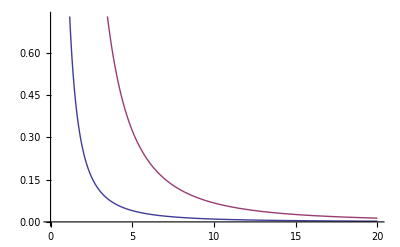

```mathematica
Plot[{1/qT^2,1/qT^2-1/qT^2 Log[qT^2/173.2^2]},{qT,0,20}]
```

## Partonic cross section 2

#### Replacements

```mathematica
ReplBetaXs={xs->(1-beta)/(1+beta),beta-> Sqrt[1-(4 mt^2)/M^2] };
ReplHShs={HSqq00-> hsqq00,HSqq10-> hsqq10,HSqq11-> hsqq11,HSqq22-> hsqq22};
```

#### HSqq^(n,m) functions

```mathematica
hsqq00=Tr[softqq[0].Hqq[0]]
```

(CF (2 t1^2 xs^2+2 mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+4 xs+xs^2)))/(mt^4 (1+xs)^4)

```mathematica
FullSimplify[M^6 √(1-(4 mt^2)/M^2)Li2[((-1+√(1-(4 mt^2)/M^2)) Tan[θ/2]^2)/(1+√(1-(4 mt^2)/M^2))],Assumptions->{M>0,mt<M}]
```

M^6 √(1-(4 mt^2)/M^2) Li2[((-M+√(M^2-4 mt^2)) Tan[θ/2]^2)/(M+√(M^2-4 mt^2))]

```mathematica
hsqq10=Tr[softqq[1].Hqq[0]]+Tr[softqq[0].Hqq[1]]/.Lp-> 0//.ReplBetaXs//Simplify
```

-1/(M^4 Nc βt)CF (M^4+2 t1^2+2 M^2 (mt^2+t1)) (-(-2+CA^2) βt Li2[1-t1^2/(M^2 mt^2)]-CA^2 βt Li2[1-(t1 u1)/(M^2 mt^2)]-2 βt Li2[1-u1^2/(M^2 mt^2)]-Li2[((-1+√(1-(4 mt^2)/M^2)) Tan[θ/2]^2)/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]-βt^2 Li2[((-1+√(1-(4 mt^2)/M^2)) Tan[θ/2]^2)/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+Li2[((1+√(1-(4 mt^2)/M^2)) Tan[θ/2]^2)/(-1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+βt^2 Li2[((1+√(1-(4 mt^2)/M^2)) Tan[θ/2]^2)/(-1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+4 CF Nc βt Log[(t1 u1)/(M^2 mt^2)]+4 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2 Log[Cos[θ/2]]+4 βt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2 Log[Cos[θ/2]])+CF (73/12+(16 mt^2)/(3 M^2)-(32 mt^4)/(3 M^4)+(21 M^2)/(4 (M^2-4 mt^2))-(9 mt^2)/(M^2-4 mt^2)+(59 π^2)/32-(7 mt^2 π^2)/(9 M^2)-(193 M^2 π^2)/(96 (M^2-4 mt^2))+(193 mt^2 π^2)/(24 (M^2-4 mt^2))-1/2 √(1-(4 mt^2)/M^2) π^2-(4 mt^2 √(1-(4 mt^2)/M^2) π^2)/(9 M^2)+(3 M^6 √(1-(4 mt^2)/M^2) π^2)/(8 (M^2-4 mt^2)^3)-(11 M^4 √(1-(4 mt^2)/M^2) π^2)/(18 (M^2-4 mt^2)^2)+(73 M^2 √(1-(4 mt^2)/M^2) π^2)/(72 (M^2-4 mt^2))+(32 t1)/(3 M^2)-(9 t1)/(2 mt^2)-(32 mt^2 t1)/(3 M^4)-(6 t1)/(M^2-4 mt^2)+(9 M^2 t1)/(2 M^2 mt^2-8 mt^4)-(π^2 t1)/(3 M^2)+(55 π^2 t1)/(48 mt^2)+(55 π^2 t1)/(12 (M^2-4 mt^2))-(55 M^2 π^2 t1)/(48 mt^2 (M^2-4 mt^2))-(13 √(1-(4 mt^2)/M^2) π^2 t1)/(18 M^2)-(√(1-(4 mt^2)/M^2) π^2 t1)/(2 mt^2)+(3 M^6 √(1-(4 mt^2)/M^2) π^2 t1)/(8 mt^2 (M^2-4 mt^2)^3)-(67 M^4 √(1-(4 mt^2)/M^2) π^2 t1)/(72 mt^2 (M^2-4 mt^2)^2)+(19 M^2 √(1-(4 mt^2)/M^2) π^2 t1)/(18 mt^2 (M^2-4 mt^2))+(32 t1^2)/(3 M^4)-(3 t1^2)/(4 mt^4)-(3 t1^2)/(M^2 mt^2)-(32 mt^2 t1^2)/(3 M^6)+(3 M^2 t1^2)/(4 mt^4 (M^2-4 mt^2))+(2 π^2 t1^2)/(9 M^4)-(4 √(1-(4 mt^2)/M^2) π^2 t1^2)/(9 M^4)-(91 √(1-(4 mt^2)/M^2) π^2 t1^2)/(288 mt^4)-(23 √(1-(4 mt^2)/M^2) π^2 t1^2)/(36 M^2 mt^2)+(3 M^6 √(1-(4 mt^2)/M^2) π^2 t1^2)/(32 mt^4 (M^2-4 mt^2)^3)-(11 M^4 √(1-(4 mt^2)/M^2) π^2 t1^2)/(32 mt^4 (M^2-4 mt^2)^2)+(163 M^2 √(1-(4 mt^2)/M^2) π^2 t1^2)/(288 mt^4 (M^2-4 mt^2))+2 Log[hscale^2/mt^2]+(4 mt^2 Log[hscale^2/mt^2])/M^2+(4 t1 Log[hscale^2/mt^2])/M^2+(4 t1^2 Log[hscale^2/mt^2])/M^4-8/3 Log[hscale^2/mt^2]^2-(16 mt^2 Log[hscale^2/mt^2]^2)/(3 M^2)-(16 t1 Log[hscale^2/mt^2]^2)/(3 M^2)-(16 t1^2 Log[hscale^2/mt^2]^2)/(3 M^4)+83/3 Log[2/(1+√(1-(4 mt^2)/M^2))]-(16 mt^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(9 M^4 Log[2/(1+√(1-(4 mt^2)/M^2))])/((M^2-4 mt^2)^2)-(74 M^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 (M^2-4 mt^2))+(436 mt^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 (M^2-4 mt^2))-(16 t1 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)+(37 t1 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 mt^2)-(9 M^4 t1 Log[2/(1+√(1-(4 mt^2)/M^2))])/(mt^2 (M^2-4 mt^2)^2)+(272 t1 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 (M^2-4 mt^2))-(10 M^2 t1 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 mt^2 (M^2-4 mt^2))-(16 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)-(21 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(4 mt^4)-(12 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(M^2 mt^2)-(9 M^4 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(4 mt^4 (M^2-4 mt^2)^2)+(15 M^2 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))])/(2 mt^4 (M^2-4 mt^2))-4/3 Log[hscale^2/mt^2] Log[2/(1+√(1-(4 mt^2)/M^2))]-(8 mt^2 Log[hscale^2/mt^2] Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(8 t1 Log[hscale^2/mt^2] Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(8 t1^2 Log[hscale^2/mt^2] Log[2/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)+10 Log[2/(1+√(1-(4 mt^2)/M^2))]^2+(44 mt^2 Log[2/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^2)+(20 t1 Log[2/(1+√(1-(4 mt^2)/M^2))]^2)/M^2+(80 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^4)-83/6 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+(8 mt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)+(9 M^4 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(2 (M^2-4 mt^2)^2)+(37 M^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 (M^2-4 mt^2))-(218 mt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 (M^2-4 mt^2))-1/2 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]-(4 mt^2 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/M^2-(16 mt^4 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)+(M^2 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 (M^2-4 mt^2))+(8 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(37 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 mt^2)+(9 M^4 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(2 mt^2 (M^2-4 mt^2)^2)-(136 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 (M^2-4 mt^2))+(5 M^2 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 mt^2 (M^2-4 mt^2))-(4 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(√(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 mt^2)-(16 mt^2 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)+(M^2 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 mt^2 (M^2-4 mt^2))+(8 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)+(21 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(8 mt^4)+(6 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(M^2 mt^2)+(9 M^4 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(8 mt^4 (M^2-4 mt^2)^2)-(15 M^2 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(4 mt^4 (M^2-4 mt^2))-(4 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)-(√(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(24 mt^4)-(√(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 M^2 mt^2)-(16 mt^2 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^6)+(M^2 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(24 mt^4 (M^2-4 mt^2))+2/3 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+(4 mt^2 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)+1/6 √(1-(4 mt^2)/M^2) Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+(2 mt^2 √(1-(4 mt^2)/M^2) Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)+(M^2 √(1-(4 mt^2)/M^2) Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(2 (M^2-4 mt^2))+(4 t1 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)+(2 √(1-(4 mt^2)/M^2) t1 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(√(1-(4 mt^2)/M^2) t1 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 mt^2)+(M^2 √(1-(4 mt^2)/M^2) t1 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 mt^2 (M^2-4 mt^2))+(4 t1^2 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)+(2 √(1-(4 mt^2)/M^2) t1^2 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)-(√(1-(4 mt^2)/M^2) t1^2 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(24 mt^4)-(√(1-(4 mt^2)/M^2) t1^2 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(6 M^2 mt^2)+(M^2 √(1-(4 mt^2)/M^2) t1^2 Log[hscale^2/mt^2] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(24 mt^4 (M^2-4 mt^2))-10 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]-(44 mt^2 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(20 t1 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/M^2-(80 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)-1/3 √(1-(4 mt^2)/M^2) Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]-(4 mt^2 √(1-(4 mt^2)/M^2) Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)-(M^2 √(1-(4 mt^2)/M^2) Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(M^2-4 mt^2)-(4 √(1-(4 mt^2)/M^2) t1 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2)+(√(1-(4 mt^2)/M^2) t1 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 mt^2)-(M^2 √(1-(4 mt^2)/M^2) t1 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 mt^2 (M^2-4 mt^2))-(4 √(1-(4 mt^2)/M^2) t1^2 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4)+(√(1-(4 mt^2)/M^2) t1^2 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(12 mt^4)+(√(1-(4 mt^2)/M^2) t1^2 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^2 mt^2)-(M^2 √(1-(4 mt^2)/M^2) t1^2 Log[(2 √(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(12 mt^4 (M^2-4 mt^2))+273/32 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2+(11 mt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^2)-(193 M^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(32 (M^2-4 mt^2))+(193 mt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(8 (M^2-4 mt^2))-13/12 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2+(mt^2 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^2)+(9 M^6 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(8 (M^2-4 mt^2)^3)-(11 M^4 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(6 (M^2-4 mt^2)^2)+(103 M^2 √(1-(4 mt^2)/M^2) Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(24 (M^2-4 mt^2))+(5 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/M^2+(55 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(16 mt^2)+(55 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(4 (M^2-4 mt^2))-(55 M^2 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(16 mt^2 (M^2-4 mt^2))-(√(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(2 M^2)-(23 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(12 mt^2)+(9 M^6 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(8 mt^2 (M^2-4 mt^2)^3)-(67 M^4 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(24 mt^2 (M^2-4 mt^2)^2)+(43 M^2 √(1-(4 mt^2)/M^2) t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(12 mt^2 (M^2-4 mt^2))+(20 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^4)+(√(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^4)-(101 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(96 mt^4)-(7 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(3 M^2 mt^2)+(9 M^6 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(32 mt^4 (M^2-4 mt^2)^3)-(33 M^4 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(32 mt^4 (M^2-4 mt^2)^2)+(173 M^2 √(1-(4 mt^2)/M^2) t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]^2)/(96 mt^4 (M^2-4 mt^2))+14/3 Log[-t1/mt^2]-(14 mt^2 Log[-t1/mt^2])/(3 M^2)+(14 t1 Log[-t1/mt^2])/(3 M^2)+(14 mt^2 Log[-t1/mt^2])/(3 (mt^2+t1))+(14 mt^4 Log[-t1/mt^2])/(3 M^2 (mt^2+t1))+28/3 Log[hscale^2/mt^2] Log[-t1/mt^2]+(56 mt^2 Log[hscale^2/mt^2] Log[-t1/mt^2])/(3 M^2)+(56 t1 Log[hscale^2/mt^2] Log[-t1/mt^2])/(3 M^2)+(56 t1^2 Log[hscale^2/mt^2] Log[-t1/mt^2])/(3 M^4)-28/3 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2]-(56 mt^2 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2])/(3 M^2)-(56 t1 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2])/(3 M^2)-(112 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2])/(3 M^4)+14/3 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2]+(28 mt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2])/(3 M^2)+(28 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2])/(3 M^2)+(56 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[-t1/mt^2])/(3 M^4)-14/3 Log[-t1/mt^2]^2-(28 mt^2 Log[-t1/mt^2]^2)/(3 M^2)-(28 t1 Log[-t1/mt^2]^2)/(3 M^2)-(4 mt^2 Log[(M^2+t1)/mt^2])/(3 M^2)-(4 t1 Log[(M^2+t1)/mt^2])/(3 M^2)-(4 mt^2 Log[(M^2+t1)/mt^2])/(3 (M^2-mt^2+t1))-(4 mt^4 Log[(M^2+t1)/mt^2])/(3 M^2 (M^2-mt^2+t1))+8/3 Log[hscale^2/mt^2] Log[(M^2+t1)/mt^2]+(16 mt^2 Log[hscale^2/mt^2] Log[(M^2+t1)/mt^2])/(3 M^2)+(16 t1 Log[hscale^2/mt^2] Log[(M^2+t1)/mt^2])/(3 M^2)+(16 t1^2 Log[hscale^2/mt^2] Log[(M^2+t1)/mt^2])/(3 M^4)-8 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2]-(16 mt^2 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2])/(3 M^2)-(16 t1 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2])/M^2-(32 t1^2 Log[2/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2])/(3 M^4)+4 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2]+(8 mt^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2])/(3 M^2)+(8 t1 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2])/M^2+(16 t1^2 Log[(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))] Log[(M^2+t1)/mt^2])/(3 M^4)+4/3 Log[(M^2+t1)/mt^2]^2-(8 mt^2 Log[(M^2+t1)/mt^2]^2)/(3 M^2)+(8 t1 Log[(M^2+t1)/mt^2]^2)/(3 M^2)-(4 (M^2-2 mt^2) √(1-(4 mt^2)/M^2) (M^4+2 t1^2+2 M^2 (mt^2+t1)) PolyLog[2,(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))])/(3 M^4 (M^2-4 mt^2))+1/(3 M^2 (M^2-4 mt^2)^3)2 √(1-(4 mt^2)/M^2) (13 M^8+M^6 (-66 mt^2+26 t1)+32 mt^4 t1 (10 mt^2+27 t1)+4 M^4 (13 mt^4-33 mt^2 t1+9 t1^2)+4 M^2 (112 mt^6+116 mt^4 t1-63 mt^2 t1^2)) PolyLog[2,(-1+√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2))]+4/3 PolyLog[2,-(M^2-mt^2+t1)/mt^2]-(8 mt^2 PolyLog[2,-(M^2-mt^2+t1)/mt^2])/(3 M^2)+(8 t1 PolyLog[2,-(M^2-mt^2+t1)/mt^2])/(3 M^2)-14/3 PolyLog[2,1+t1/mt^2]-(28 mt^2 PolyLog[2,1+t1/mt^2])/(3 M^2)-(28 t1 PolyLog[2,1+t1/mt^2])/(3 M^2))

```mathematica
hsqq11=Plus@@Cases[Tr[softqq[1].Hqq[0]]+Tr[softqq[0].Hqq[1]],fac_ Lp-> fac,-1]
```

4 CF Nc βt+8 βt Log[-t1/(M mt)]-4 CA^2 βt Log[-t1/(M mt)]-8 βt Log[-u1/(M mt)]-Log[xs]-βt^2 Log[xs]

```mathematica
hsqq22=Plus@@Cases[Expand[Tr[softqq[2].Hqq[0]]+Tr[softqq[0].Hqq[2]]+Tr[softqq[1].Hqq[1]]],fac_ Power[Lp,2]-> fac,-1]//Simplify
```

-1/(18 mt^4 Nc (1+xs)^4 βt^2)CF (2 t1^2 xs^2+2 mt^2 t1 xs (1+xs)^2+mt^4 (1+xs)^2 (1+4 xs+xs^2)) (-192 CF Nc βt^2-36 CF Nc β0 βt^2-96 CF Nc βt^2 Log[t1/u1]+384 βt^2 Log[-u1/(M mt)]+72 β0 βt^2 Log[-u1/(M mt)]+192 βt^2 Log[t1/u1] Log[-u1/(M mt)]+128 CA βt^2 Log[t1/u1] Log[-u1/(M mt)]+48 βt Log[xs]+9 β0 βt Log[xs]+48 βt^3 Log[xs]+9 β0 βt^3 Log[xs]+24 βt Log[t1/u1] Log[xs]+24 βt^3 Log[t1/u1] Log[xs]-108 βt Log[-t1/(mt Mtt)] (-4 CF Nc βt+8 βt Log[-u1/(M mt)]+(1+βt^2) Log[xs])+12 CF Nc βt Log[(1-βt)/(1+βt)]+12 CF Nc βt^3 Log[(1-βt)/(1+βt)]-24 βt Log[-u1/(M mt)] Log[(1-βt)/(1+βt)]-24 βt^3 Log[-u1/(M mt)] Log[(1-βt)/(1+βt)]-3 Log[xs] Log[(1-βt)/(1+βt)]-6 βt^2 Log[xs] Log[(1-βt)/(1+βt)]-3 βt^4 Log[xs] Log[(1-βt)/(1+βt)]-4 βt Log[-t1/(M mt)] (108 (-2+CA^2) βt Log[-t1/(mt Mtt)]-8 (-6-4 CA+3 CA^2) βt Log[t1/u1]+3 (-2+CA^2) (-(16+3 β0) βt+(1+βt^2) Log[(1-βt)/(1+βt)])))

#### Partonic cross section

```mathematica
C2qq2tt[z_,qT_,M_,mt_,theta_, μ_]:=(
Sigmaqqbar["qqbar",2,2] 1/qT^2 Log[qT^2/μ^2]+
Sigmaqqbar["qqbar",2,3] 1/qT^2 Log[qT^2/μ^2]^2+
Sigmaqqbar["qqbar",2,4] 1/qT^2 Log[qT^2/μ^2]^3
)//.ReplHShs//.ReplBetaXs(*//Simplify*)
```

```mathematica
C2qq2tt[z,qT,M,mt,theta, μ]
```

(8 CF^3 (mt^4 (1+(1-√(1-(4 «1»)/(«1»)))/(1+√(1-(4 «1»)/(«1»))))^2 (1+((1-√(1-(4 «1»)/M^2))^2)/((1+√(1-(4 «1»)/M^2))^2)+(4 (1-√(1-(4 mt^2)/M^2)))/(1+√(1-(4 mt^2)/M^2)))+(2 mt^2 (1-√(1-«1»)) (1+«1»)^2 t1)/(1+√(1-(4 «1»)/M^2))+(2 (1-√(1-(«1»)/(«1»)))^2 t1^2)/(1+√(1-(«1»)/(«1»)))^2) DiracDelta[-1+z] Log[qT^2/μ^2]^3)/(mt^4 (1+(1-√(1-(4 mt^2)/M^2))/(1+√(1-(4 mt^2)/M^2)))^4 qT^2)+(16 («1»)^2 (3/8 CF DiracDelta[-1+z] («1»)+(CF («1») («1»))/(mt^4 («1»)^4)))/qT^2+(16 Log[qT^2/μ^2] (-(CF («1») DiracDelta[-1+z] («1»))/(144 mt^4 (1+(«1»)/(«1»))^4 Nc βt^2)+«4»))/qT^2

```mathematica
WriteString[f1,"\n  double val = ",ToString[MyCForm[tmp]],";\n\n"];
```

```mathematica
ReplHSqq2={fac_ Log[a_]^(n_.):> Simplify[fac] Log[Simplify[a]]^n,ac_ PolyLog[n_,a_]^(n_.):> Simplify[fac] PolyLog[n,Simplify[a]]^n};
(*ReplSimplifyHS={Mtt-> M, fac_.Log[a__]->(fac/.xs:> (1-βt)/(1+βt))Log[a]};*)
```

```mathematica
(*hsqq22=(Plus@@Cases[HSqq2//Expand,fac_ Lp^2-> fac,-1])//.ReplHSqq2//.ReplNumbers//.{Mtt-> M}//.{Log[t1/u1] -> Log[-t1/(M mt)] -Log[-u1/(M mt)]}//.{ xs:> (1-βt)/(1+βt)}//. Log[(1-βt)/(1+βt)]-> Log[xs]//FullSimplify*)
hsqq21=Plus@@Cases[HSqq2//Expand,fac_ Lp-> fac,-1]//.ReplHSqq2//.ReplNumbers//.{Mtt-> M}//.{Log[t1/u1] -> Log[-t1/(M mt)] -Log[-u1/(M mt)],hscale-> mt}//.{ xs:> (1-βt)/(1+βt)}//. {Log[(1-βt)/(1+βt)]^(n_.)-> Log[xs]^n,PolyLog[m_,a_]^(n_.)-> PolyLog[m,Simplify[a/.βt:> (1-xs)/(1+xs)]^n]}//Simplify;
```

$Aborted

```mathematica
ReplNotationIinitial={Log[-t1/mt^2]^(n_.)-> n Log[-t1/mt^2],Log[(M^2+t1)/mt^2]^(n_.)-> n Log[(M^2+t1)/mt^2],PolyLog[2,-(1-βt)/(1+βt)]-> PolyLog[2,(-1+βt)/(1+βt)]};
ReplShortNotation={Log[-t1/(M mt)] -> Lt1,Log[-u1/(M mt)] -> Lu1,PolyLog[2,(1-βt)/(1+βt)]-> Li2xs,  PolyLog[2,(-1+βt)/(1+βt)]-> Li2mxs,PolyLog[2,1+t1/mt^2]-> L2t1,Log[-t1/mt^2]-> Lt1mt,Log[(M^2+t1)/mt^2]-> Lt1M,Log[2/(1+βt)]-> Lxsp1, Log[(2 βt)/(1+βt)]-> Lxsm1, Log[xs]-> Lxs, PolyLog[2,-(M^2-mt^2+t1)/mt^2]-> Li21M };
hsqq21//.ReplNotationIinitial//.ReplShortNotation//Simplify;
```

```mathematica
ReplNotationRev=Reverse/@ReplShortNotation;
```

```mathematica
f1=OpenWrite["integrator/hs.hh",PageWidth-> 1000];
WriteString[f1,"double hsqq10("
Do[
WriteString[f1,"double " <> ToString[CForm[ReplNotationRev[[i]][[1]]]]<>" = "<>ToString[CForm[ReplNotationRev[[i]][[2]]]]<>";\n"];
,{i,1,Length[ReplNotationRev]}
]
Close[f1];
```